```mathematica
ClearAll["Global`*"]
```

```mathematica
Wave Function
```

```mathematica
ψ[x_]:=(ⅇ^(-x^2/2))/π^(1/4) (√(1+√2 λ))/(1+√2 λ (1+Erf[x])/2)
dψ[x_]:=D[ψ[x],{x,1}]
ddψ[x_]:=D[ψ[x],{x,2}]
```

```mathematica
Entropy
```

```mathematica
h[t_]:=(t+1/2) Log[t+1/2]+(t-1/2) Log[t-1/2]

X:=∫_(-∞)^∞ x ψ[x]^2 ⅆx
P:=-I∫_(-∞)^∞ ψ[x]  dψ[x]ⅆx
X2:=∫_(-∞)^∞ x^2 ψ[x]^2 ⅆx
P2:=-∫_(-∞)^∞ ψ[x] ddψ[x]ⅆx
XP:=-I∫_(-∞)^∞ x ψ[x] dψ[x]ⅆx
PX:=-I∫_(-∞)^∞ ψ[x] (ψ[x]+x  dψ[x])ⅆx

σ:=({{X2-X^2, 1/2(XP+PX)-X P}, {1/2(XP+PX)-X P, P2-P^2}})
t=√Det[σ] ;
```

$Aborted

```mathematica
Rough
```

```mathematica
Integrate[ψ[x]   D[ ψ[x],{x,1}],{x,-∞,∞}]
```

∫_(-∞)^∞ ψ[x] ψ'[x]ⅆx

```mathematica
Example
```

```mathematica
σ//MatrixForm
```

(-λ^2/π+(2 √3 λ^2+π (6+λ^2))/(12 π) | 1/2 (-1/12 ⅈ (-6-λ^2)-1/12 ⅈ (6+λ^2))
1/2 (-1/12 ⅈ (-6-λ^2)-1/12 ⅈ (6+λ^2)) | (6 √3 λ^2+π (6+λ^2))/(12 π))

```mathematica
h[t]
```

(-1/2+√(1/4+λ^2/12-λ^2/(2 π)+λ^2/(√3 π)+λ^4/144+λ^4/(4 π^2)-(√3 λ^4)/(2 π^2)-λ^4/(12 π)+λ^4/(6 √3 π))) Log[-1/2+√(1/4+λ^2/12-λ^2/(2 π)+λ^2/(√3 π)+λ^4/144+λ^4/(4 π^2)-(√3 λ^4)/(2 π^2)-λ^4/(12 π)+λ^4/(6 √3 π))]+(1/2+√(1/4+λ^2/12-λ^2/(2 π)+λ^2/(√3 π)+λ^4/144+λ^4/(4 π^2)-(√3 λ^4)/(2 π^2)-λ^4/(12 π)+λ^4/(6 √3 π))) Log[1/2+√(1/4+λ^2/12-λ^2/(2 π)+λ^2/(√3 π)+λ^4/144+λ^4/(4 π^2)-(√3 λ^4)/(2 π^2)-λ^4/(12 π)+λ^4/(6 √3 π))]

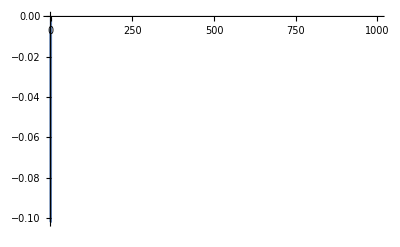

```mathematica
Plot[%35,{λ,0.1,1000}]
```